# Debugger and Unit test helper

This notebook contains a set of tools to evaluate expected va

## Gubser Calculator

The Gubser solution is a solution for viscous hydrodynamic (without Bulk) in 2+1 D. The functions below allow one to evaluate the solution in a given point tau0, x0, y0. We can use this to compare to variables in the code. 

We first declare the points of evaluation

```mathematica
x0=-2.3; (*fm*)
y0=2.3;(*fm*)
tau0=1;(*fm*)
```

Below, are the constants being used in the code

```mathematica
ℏc=(197.326980/1000);  (*GeV fm*)
ηOverS=0.2;
α=3 π^2/90 (2(Nc^2-1)+7/2 Nc Nf)/.{Nc->3,Nf->2.5};
c=5;(*Related to the shear relaxation constant*)
```

Then, we will solve some differential equations

```mathematica
a=1/3;
e[ρ_]:=α (T hat[ρ])^4 Cosh[(μ hat[ρ])/(T hat[ρ])];
p[ρ_]:=a e[ρ];
n[ρ_]:=a α (T hat[ρ])^3 Sinh[(μ hat[ρ])/(T hat[ρ])];
s[ρ_]:=a α (T hat[ρ])^2(4T hat[ρ]Cosh[(μ hat[ρ])/(T hat[ρ])]-μ hat[ρ]Sinh[(μ hat[ρ])/(T hat[ρ])]);
sol=Solve[{(1/(e[ρ]+p[ρ])(D[e[ρ],ρ]+2(e[ρ]+p[ρ])Tanh[ρ]-π bar ηη[ρ](e[ρ]+p[ρ])Tanh[ρ])//FullSimplify)==0,
(1/(e[ρ]+p[ρ])(D[n[ρ],ρ]+2n[ρ]Tanh[ρ])//FullSimplify)==0},{T hat'[ρ], μ hat'[ρ]}];
ConservEqs=(%/.Rule->Equal//FullSimplify)[[1]];
D[π bar ηη[ρ],ρ]+(π bar ηη[ρ])/(e[ρ]+p[ρ])D[e[ρ]+p[ρ],ρ]+1/τR π bar ηη[ρ]-(4/(3c)(s[ρ]T hat[ρ])/(e[ρ]+p[ρ])Tanh[ρ]-8/3 π bar ηη[ρ]Tanh[ρ])-0/(35τR)(π bar ηη[ρ])^2 -10/21 π bar ηη[ρ]Tanh[ρ];
(%/.sol)[[1]]//FullSimplify;
piEq=(%/.τR->c ηOverS/T hat[ρ])==0;
sols=NDSolve[{
ConservEqs[[1]],
ConservEqs[[2]],
piEq,
T hat[0]==1.2 (*0.31532/ℏc*),
μ hat[0]==1.2 (*0.162056/ℏc *),
π bar ηη[0]==0.0},
{T hat,μ hat,π bar ηη},
{ρ,-12,212}
];
```

Lastly, we change to Cartesian coordinates

```mathematica
ρ[τ_,r_]:=ArcSinh[-((1-τ^2+r^2)/(2τ))];
T[τ_,r_]:=ℏc ((T hat[ρ[τ,r]]/.sols)/τ)[[1]];
T[τ_,x_,y_]:= T[τ,Sqrt[x^2+y^2]];
u r[τ_,r_]:=Sinh[ArcTanh[(2τ r)/(1+τ^2+r^2)]];
u x[τ_,x_,y_]:=Piecewise[{{x/Sqrt[x^2+y^2] Sinh[ArcTanh[(2τ Sqrt[x^2+y^2])/(1+τ^2+x^2+y^2)]],Sqrt[x^2+y^2]!=0},{0.0,Sqrt[x^2+y^2]==0}}];
u y[τ_,x_,y_]:=Piecewise[{{y/Sqrt[x^2+y^2] Sinh[ArcTanh[(2τ Sqrt[x^2+y^2])/(1+τ^2+x^2+y^2)]],Sqrt[x^2+y^2]!=0},{0.0,Sqrt[x^2+y^2]==0}}];
π hat ηη[τ_,r_]:=4/3 α ℏc ((T hat[ρ[τ,r]]/.sols)[[1]])^4 (π bar ηη[ρ[τ,r]]/.sols)[[1]]; 
π ηη[τ_,x_,y_]:=1/τ^6 π hat ηη[τ,Sqrt[x^2+y^2]];
π xx[τ_,x_,y_]:=-(1/2) 1/τ^4 (1+Piecewise[{{(x/Sqrt[x^2+y^2])^2 Sinh[ArcTanh[(2τ Sqrt[x^2+y^2])/(1+τ^2+x^2+y^2)]]^2,x^2+y^2!=0},{0.0,x^2+y^2==0}}])π hat ηη[τ,Sqrt[x^2+y^2]];
π yy[τ_,x_,y_]:=-(1/2) 1/τ^4 (1+Piecewise[{{(y/Sqrt[x^2+y^2])^2 Sinh[ArcTanh[(2τ Sqrt[x^2+y^2])/(1+τ^2+x^2+y^2)]]^2,x^2+y^2!=0},{0.0,x^2+y^2==0}}])π hat ηη[τ,Sqrt[x^2+y^2]];
π xy[τ_,x_,y_]:=Piecewise[{{-(1/2) 1/τ^4 (x y )/(x^2+y^2) Sinh[ArcTanh[(2τ Sqrt[x^2+y^2])/(1+τ^2+x^2+y^2)]]^2 π hat ηη[τ,Sqrt[x^2+y^2]],x^2+y^2!=0},{0.0,x^2+y^2==0}}];
ut[τ_,x_,y_]:=√(1+(u x[τ,x,y])^2+(u y[τ,x,y])^2)
vx[τ_,x_,y_]:=(u x[τ,x,y])/ut[τ,x,y]
vy[τ_,x_,y_]:=(u y[τ,x,y])/ut[τ,x,y]
```

We also evaluate other thermodynamic quantities, using a conformal EoS. This is defined as

p(T) = KP (T/T0)^4

When using natural units, T0 = 1 fm^-1 and KP= K0*T0^4. K0 is a dimensionless constant. Below, we use this prescription to evaluate energy density, entropy, temperature and pressure using this EoS

```mathematica
K0=4.633231;
T0=1;(*fm^-1*)
T0GeV=ℏc;(*T0=1 fm^-1 ~ .197 GeV*)
KP=K0*T0^4; (*fm^-4*)
e[τ_,x_,y_]:=3KP(T[τ,x,y]/T0GeV)^4 (*fm^-4*);
s[τ_,x_,y_]:=4KP(T[τ,x,y]/T0GeV)^3/T0;
p[τ_,x_,y_]:=KP(T[τ,x,y]/T0GeV)^4;
sStar[τ_,x_,y_]:= s[τ,x,y]*ut[τ,x,y];
```

I will also define the Ideal Gubser solution, for comparison. We plot them for reference.

```mathematica
TIdeal[τ_,r_]=((2τ)^(2/3)*T[1,0,0])/(τ(1+2(τ^2+r^2)+(τ^2-r^2)^2)^(1/3));
TIdeal[τ_,x_,y_]=TIdeal[τ,√(x^2+y^2)];
```

```mathematica
Animate[Plot[{3T[τ,x,0]/T[1,0,0],3TIdeal[τ,x,0]/T[1,0,0],u x[τ,x,0]},{x,-5,5},PlotRange->3],{τ,.1,3}]
```

Lastly, we print the values of thermodynamic quantities. Use this to Debug the code, particularly the values of smoothed entropy and the quantities inside hydro and thermo structs

```mathematica
x0=-.62; y0=.62;
Print["Expected input energy: " ,e[tau0,x0,y0]," fm^-4"]
Print["Expected input entropy: " ,s[tau0,x0,y0]," fm^-3"]
Print["Expected smoothed entropy: " ,sStar[tau0,x0,y0]," fm^-3"]
Print["Expected norm_spec entropy: " ,sStar[tau0,x0,y0]*(.05)^2," fm^-3 - Assumes initial particle in .02 spacing"]
Print["Expected pressure: " ,p[tau0,x0,y0]," fm^-4"]
Print["Expected pressure: " ,p[tau0,x0,y0]*ℏc*1000," MeV/fm^3"]
Print["Expected pressure: " ,p[tau0,x0,y0]*ℏc*(1.6022*10^-10)/10^-45," Pa"]
Print["Expected pressure: " ,p[tau0,x0,y0]*ℏc*(1.6022*10^-10)/10^-45/101325," atm"]
Print["Expected temperature: " ,T[tau0,x0,y0]/ℏc," fm^-1"]
Print["Expected temperature: " ,T[tau0,x0,y0]," GeV"]
Print["Expected gamma: " ,ut[tau0,x0,y0]," GeV"]
Print["Expected ux: " ,u x[tau0,x0,y0]," GeV"]
Print["Expected uy: " ,u y[tau0,x0,y0]," GeV"]
```

Expected input energy: 24.0175 fm^-4

Expected input entropy: 27.9309 fm^-3

Expected smoothed entropy: 36.0928 fm^-3

Expected norm_spec entropy: 0.090232 fm^-3 - Assumes initial particle in .02 spacing

Expected pressure: 8.00582 fm^-4

Expected pressure: 1579.76 MeV/fm^3

Expected pressure: 2.5311×10^35 Pa

Expected pressure: 2.498×10^30 atm

Expected temperature: 1.14652 fm^-1

Expected temperature: 0.226239 GeV

Expected gamma: 1.29222 GeV

Expected ux: -0.578716 GeV

Expected uy: 0.578716 GeV

We can also compute the expected values of gradients

```mathematica
gradP[τ_,x_,y_]=Grad[p[τ,x,y],{x,y}];
gradE[τ_,x_,y_]=Grad[e[τ,x,y],{x,y}];
gradV[τ_,x_,y_]={Grad[vx[τ,x,y],{x,y}],Grad[vy[τ,x,y],{x,y}]};
uu[τ_,x_,y_]={{(u x[τ,x,y])^2,u x[τ,x,y]*u y[τ,x,y]},{u x[τ,x,y]*u y[τ,x,y],(u y[τ,x,y])^2}};
```

```mathematica
gradP[tau0,x0,y0]
gradE[tau0,x0,y0]
gradV[tau0,x0,y0]
uu[tau0,x0,y0]
π ηη[tau0,x0,y0]
```

{4.36386,-4.36386}

{13.0916,-13.0916}

{{0.521767,0.200567},{0.200567,0.521767}}

{{0.334912,-0.334912},{-0.334912,0.334912}}

0.111428

Below, we will also find the FO surface

{}

InterpolatingFunction::dmval: Input value {-17.9448} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-21.3402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

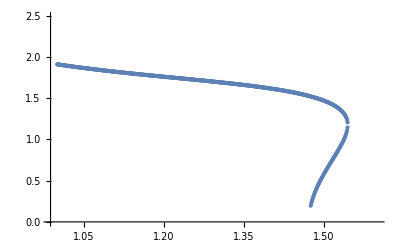

```mathematica
e[τ_,r_]:=3KP(T[τ,r]/T0GeV)^4 (*fm^-4*);
eFO = 1/ℏc;
tauf=1.6;
dt=.001;
NInter=200;
r0=r/.ResourceFunction["NewtonMethod"] [e[1,r]-eFO,{r,1.8},NInter];
Sols={}
For[t=1.,t<tauf,t=t+dt,
r0=r/.ResourceFunction["NewtonMethod"] [e[t,r]-eFO,{r,r0},NInter];
AppendTo[Sols,{t,r0}];
]
r0=r/.ResourceFunction["NewtonMethod"] [e[1.475,r]-eFO,{r,.5},NInter];
For[t=1.475,t<tauf,t=t+dt,
r0=r/.ResourceFunction["NewtonMethod"] [e[t,r]-eFO,{r,r0},NInter];
AppendTo[Sols,{t,r0}];
]
ListPlot[Sols]
```

```mathematica
HypersurfacePoints=Table[{Sols[[i]][[2]]Cos[θ],Sols[[i]][[2]]Sin[θ],Sols[[i]][[1]]},{i,1,Length[Sols]},{θ,0,2Pi,2Pi/200}];
```

```mathematica
GubserHypersurface =ArrayReshape [HypersurfacePoints,{726*201,3}]
ListPointPlot3D[GubserHypersurface ,PlotRange->{{-2,2},{-2,2},{1,1.55}},PlotStyle->{Blue,PointSize[Tiny]},AxesLabel->{"x (fm)","y (fm)", "τ (fm/c)"}]
```

-Graphics3D-

I now look for the normal vectors. This is done by evaluating the gradients of the energy density

```mathematica
nt[τ_,r_]=D[e[τ,r],τ];
nr[τ_,r_]=D[e[τ,r],r];
```

```mathematica
scaleArrows=.01;
numStopsTheta=50;
numStopsTime=1;
normals=Table[{-nr[##],-nt[##]}& @@Sols[[i]],{i,1,Length[Sols],numStopsTime}];
points=Table[{##[[2]],##[[1]]}& @Sols[[i]],{i,1,Length[Sols],numStopsTime}];
arrowTips=points+normals*scaleArrows;
arrowData=Table[Arrow[{points[[i]],arrowTips[[i]]}],{i,1,Length[points]}];
points3D=ArrayReshape[Table[
{##[[1]]*Cos[θ],##[[1]]*Sin[θ],##[[2]]}& @points[[i]],
{θ,0,2Pi-2Pi/numStopsTheta,2Pi/numStopsTheta},{i,1,Length[points]}],{Length[points]*numStopsTheta,3}];
normals3D=ArrayReshape[Table[
{##[[1]]*Cos[θ],##[[1]]*Sin[θ],##[[2]]}& @normals[[i]],
{θ,0,2Pi-2Pi/numStopsTheta,2Pi/numStopsTheta},{i,1,Length[normals]}],{Length[normals]*numStopsTheta,3}];
arrowTips3D=points3D+normals3D*scaleArrows;
arrowData3D=Table[Arrow[{points3D[[i]],arrowTips3D[[i]]}],{i,1,Length[points3D]}];
```

InterpolatingFunction::dmval: Input value {-34.6037} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
arrowData3D=Table[Arrow[{points3D[[i]],arrowTips3D[[i]]}],{i,1,Length[points3D]}];
Show[
ListPointPlot3D[GubserHypersurface ,PlotRange->{{-2,2},{-2,2},{1,1.55}},PlotStyle->{Red,PointSize[Tiny]},AxesLabel->{"x (fm)","y (fm)", "τ (fm/c)"}],
Graphics3D[{Blue,Arrowheads[Medium],arrowData3D},PlotRange->{{-2,2},{-2,2},{1,1.6}}]
]
```

-Graphics3D-

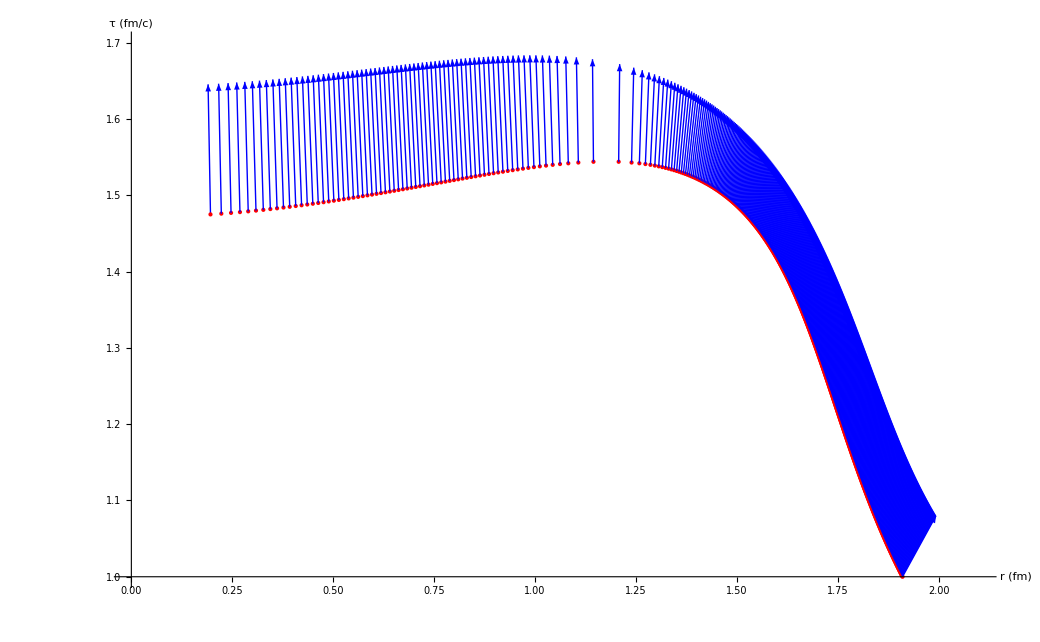

```mathematica
Show[
ListPlot[
Table[
{Sols[[i]][[2]],Sols[[i]][[1]]},{i,1,Length[Sols]}],AxesLabel->{"r (fm)","τ (fm/c)"},PlotStyle->{Red,PointSize[Small]},PlotRange->{{0,2.1},{1,1.7}} ],
Graphics[{Blue,Arrowheads[Medium],arrowData}
]]
```

```mathematica
normals//TableForm
```

8.29941 | 7.99897
8.30564 | 7.97922
8.31184 | 7.95954
8.31801 | 7.93994
8.32413 | 7.92041
8.33022 | 7.90096
8.33628 | 7.88157
8.34229 | 7.86226
8.34827 | 7.84302
8.35422 | 7.82385
8.36013 | 7.80475
8.366 | 7.78572
8.37184 | 7.76676
8.37764 | 7.74787
8.38341 | 7.72905
8.38914 | 7.7103
8.39483 | 7.69162
8.4005 | 7.673
8.40612 | 7.65445
8.41171 | 7.63597
8.41727 | 7.61756
8.4228 | 7.59921
8.42829 | 7.58093
8.43374 | 7.56271
8.43916 | 7.54457
8.44455 | 7.52648
8.44991 | 7.50846
8.45523 | 7.49051
8.46051 | 7.47262
8.46577 | 7.45479
8.47099 | 7.43703
8.47616 | 7.41935
8.48129 | 7.40175
8.48638 | 7.38423
8.49143 | 7.36678
8.49643 | 7.34941
8.50139 | 7.33212
8.50631 | 7.3149
8.51118 | 7.29776
8.51602 | 7.28069
8.52081 | 7.2637
8.52556 | 7.24678
8.53027 | 7.22993
8.53494 | 7.21316
8.53957 | 7.19646
8.54416 | 7.17983
8.54871 | 7.16327
8.55322 | 7.14679
8.55768 | 7.13037
8.56211 | 7.11403
8.5665 | 7.09776
8.57085 | 7.08156
8.57516 | 7.06542
8.57943 | 7.04936
8.58366 | 7.03337
8.58785 | 7.01744
8.592 | 7.00158
8.59612 | 6.98579
8.60019 | 6.97007
8.60423 | 6.95442
8.60823 | 6.93883
8.61219 | 6.9233
8.61611 | 6.90785
8.62 | 6.89246
8.62385 | 6.87713
8.62765 | 6.86189
8.6314 | 6.84672
8.63511 | 6.83163
8.63877 | 6.81662
8.64238 | 6.80169
8.64594 | 6.78684
8.64946 | 6.77207
8.65293 | 6.75737
8.65635 | 6.74275
8.65973 | 6.72821
8.66306 | 6.71375
8.66634 | 6.69935
8.66958 | 6.68504
8.67277 | 6.6708
8.67592 | 6.65663
8.67902 | 6.64254
8.68208 | 6.62853
8.68509 | 6.61458
8.68806 | 6.60071
8.69099 | 6.58691
8.69386 | 6.57319
8.6967 | 6.55953
8.69949 | 6.54595
8.70224 | 6.53244
8.70494 | 6.519
8.7076 | 6.50563
8.71022 | 6.49233
8.71279 | 6.4791
8.71532 | 6.46594
8.71781 | 6.45284
8.72025 | 6.43982
8.72265 | 6.42687
8.72501 | 6.41398
8.72733 | 6.40116
8.72961 | 6.38841
8.73184 | 6.37572
8.73402 | 6.36312
8.73615 | 6.3506
8.73823 | 6.33816
8.74026 | 6.3258
8.74223 | 6.31352
8.74415 | 6.30132
8.74602 | 6.2892
8.74784 | 6.27716
8.7496 | 6.26519
8.75132 | 6.25331
8.75299 | 6.2415
8.7546 | 6.22978
8.75617 | 6.21812
8.75768 | 6.20655
8.75914 | 6.19505
8.76056 | 6.18363
8.76192 | 6.17228
8.76324 | 6.16101
8.76451 | 6.14982
8.76572 | 6.1387
8.76689 | 6.12765
8.76801 | 6.11668
8.76908 | 6.10578
8.77011 | 6.09495
8.77108 | 6.0842
8.77201 | 6.07351
8.77289 | 6.06291
8.77372 | 6.05237
8.7745 | 6.0419
8.77524 | 6.03151
8.77593 | 6.02118
8.77657 | 6.01093
8.77716 | 6.00075
8.77771 | 5.99063
8.77821 | 5.98059
8.77867 | 5.97062
8.77908 | 5.96071
8.77943 | 5.95089
8.77973 | 5.94115
8.77996 | 5.93149
8.78015 | 5.92192
8.78027 | 5.91243
8.78034 | 5.90302
8.78035 | 5.89369
8.78031 | 5.88445
8.78021 | 5.87528
8.78006 | 5.86619
8.77985 | 5.85719
8.77959 | 5.84826
8.77927 | 5.83941
8.77889 | 5.83065
8.77846 | 5.82196
8.77798 | 5.81334
8.77744 | 5.80481
8.77685 | 5.79635
8.77621 | 5.78797
8.77551 | 5.77967
8.77475 | 5.77145
8.77395 | 5.7633
8.77309 | 5.75522
8.77218 | 5.74723
8.77121 | 5.7393
8.77019 | 5.73146
8.76912 | 5.72368
8.768 | 5.71599
8.76682 | 5.70836
8.7656 | 5.70081
8.76432 | 5.69333
8.76298 | 5.68593
8.7616 | 5.6786
8.76016 | 5.67134
8.75868 | 5.66416
8.75714 | 5.65704
8.75555 | 5.65
8.7539 | 5.64305
8.75218 | 5.63618
8.75041 | 5.6294
8.74857 | 5.6227
8.74667 | 5.61608
8.74472 | 5.60955
8.7427 | 5.6031
8.74063 | 5.59673
8.73849 | 5.59044
8.7363 | 5.58424
8.73404 | 5.57811
8.73173 | 5.57207
8.72936 | 5.56611
8.72693 | 5.56023
8.72444 | 5.55442
8.72189 | 5.5487
8.71929 | 5.54306
8.71662 | 5.5375
8.7139 | 5.53201
8.71112 | 5.52661
8.70828 | 5.52128
8.70539 | 5.51603
8.70244 | 5.51086
8.69943 | 5.50577
8.69636 | 5.50075
8.69323 | 5.49581
8.69005 | 5.49095
8.68681 | 5.48617
8.68352 | 5.48146
8.68017 | 5.47683
8.67676 | 5.47227
8.67328 | 5.4678
8.66975 | 5.46342
8.66615 | 5.45912
8.66248 | 5.45491
8.65875 | 5.45078
8.65496 | 5.44674
8.6511 | 5.44278
8.64718 | 5.43891
8.64319 | 5.43512
8.63914 | 5.43142
8.63503 | 5.4278
8.63085 | 5.42426
8.62661 | 5.42081
8.62231 | 5.41744
8.61795 | 5.41415
8.61352 | 5.41095
8.60903 | 5.40783
8.60447 | 5.40479
8.59986 | 5.40184
8.59518 | 5.39896
8.59044 | 5.39617
8.58563 | 5.39346
8.58077 | 5.39083
8.57584 | 5.38828
8.57085 | 5.38581
8.5658 | 5.38342
8.56068 | 5.38112
8.5555 | 5.37889
8.55027 | 5.37675
8.54497 | 5.37468
8.5396 | 5.3727
8.53417 | 5.37081
8.52866 | 5.369
8.52309 | 5.36729
8.51745 | 5.36567
8.51174 | 5.36413
8.50596 | 5.36269
8.50011 | 5.36133
8.49419 | 5.36006
8.48821 | 5.35888
8.48215 | 5.35779
8.47603 | 5.35678
8.46984 | 5.35586
8.46358 | 5.35503
8.45725 | 5.35429
8.45085 | 5.35363
8.44439 | 5.35307
8.43785 | 5.35258
8.43125 | 5.35219
8.42458 | 5.35188
8.41784 | 5.35166
8.41104 | 5.35152
8.40416 | 5.35147
8.39722 | 5.35151
8.39021 | 5.35163
8.38313 | 5.35184
8.37598 | 5.35213
8.36877 | 5.35251
8.36149 | 5.35298
8.35414 | 5.35353
8.34672 | 5.35417
8.33922 | 5.3549
8.33166 | 5.35572
8.32401 | 5.35664
8.3163 | 5.35765
8.3085 | 5.35876
8.30063 | 5.35996
8.29269 | 5.36125
8.28467 | 5.36264
8.27658 | 5.36412
8.26841 | 5.3657
8.26017 | 5.36736
8.25185 | 5.36913
8.24346 | 5.37098
8.235 | 5.37293
8.22645 | 5.37497
8.21784 | 5.3771
8.20914 | 5.37933
8.20038 | 5.38165
8.19153 | 5.38406
8.18262 | 5.38656
8.17363 | 5.38916
8.16456 | 5.39185
8.15541 | 5.39463
8.1462 | 5.39751
8.1369 | 5.40048
8.12754 | 5.40354
8.11809 | 5.40669
8.10857 | 5.40994
8.09898 | 5.41328
8.08931 | 5.41671
8.07956 | 5.42024
8.06972 | 5.42387
8.05981 | 5.4276
8.04981 | 5.43143
8.03973 | 5.43537
8.02957 | 5.4394
8.01932 | 5.44354
8.009 | 5.44777
7.99859 | 5.45211
7.98809 | 5.45654
7.97752 | 5.46108
7.96686 | 5.46572
7.95612 | 5.47046
7.9453 | 5.4753
7.93439 | 5.48024
7.9234 | 5.48528
7.91232 | 5.49043
7.90116 | 5.49567
7.88992 | 5.50102
7.8786 | 5.50647
7.86719 | 5.51201
7.8557 | 5.51767
7.84412 | 5.52342
7.83246 | 5.52927
7.82071 | 5.53523
7.80888 | 5.54129
7.79696 | 5.54745
7.78496 | 5.55371
7.77287 | 5.56007
7.7607 | 5.56654
7.74844 | 5.57312
7.73608 | 5.57981
7.72363 | 5.58661
7.7111 | 5.59351
7.69847 | 5.60053
7.68575 | 5.60766
7.67293 | 5.6149
7.66003 | 5.62224
7.64703 | 5.6297
7.63394 | 5.63727
7.62075 | 5.64496
7.60747 | 5.65275
7.5941 | 5.66065
7.58064 | 5.66867
7.56708 | 5.6768
7.55342 | 5.68504
7.53967 | 5.6934
7.52583 | 5.70186
7.51189 | 5.71044
7.49786 | 5.71914
7.48373 | 5.72794
7.4695 | 5.73687
7.45518 | 5.7459
7.44076 | 5.75505
7.42625 | 5.76432
7.41164 | 5.7737
7.39693 | 5.78319
7.38212 | 5.79281
7.36721 | 5.80254
7.3522 | 5.81239
7.33708 | 5.82236
7.32187 | 5.83246
7.30654 | 5.84268
7.29112 | 5.85302
7.27559 | 5.86349
7.25995 | 5.87408
7.24421 | 5.8848
7.22836 | 5.89564
7.21241 | 5.9066
7.19635 | 5.91769
7.18018 | 5.92891
7.16391 | 5.94026
7.14753 | 5.95173
7.13104 | 5.96333
7.11444 | 5.97505
7.09773 | 5.98691
7.08091 | 5.9989
7.06398 | 6.01101
7.04693 | 6.02326
7.02978 | 6.03564
7.01252 | 6.04815
6.99514 | 6.06079
6.97765 | 6.07356
6.96004 | 6.08647
6.94232 | 6.09951
6.92449 | 6.11269
6.90653 | 6.126
6.88846 | 6.13946
6.87027 | 6.15306
6.85195 | 6.16679
6.83352 | 6.18067
6.81497 | 6.19469
6.79629 | 6.20885
6.77749 | 6.22316
6.75857 | 6.23761
6.73952 | 6.2522
6.72035 | 6.26695
6.70106 | 6.28183
6.68163 | 6.29687
6.66208 | 6.31205
6.64241 | 6.32738
6.6226 | 6.34287
6.60266 | 6.3585
6.5826 | 6.37429
6.5624 | 6.39023
6.54207 | 6.40632
6.5216 | 6.42258
6.501 | 6.43899
6.48027 | 6.45555
6.4594 | 6.47228
6.43839 | 6.48917
6.41724 | 6.50621
6.39595 | 6.52343
6.37452 | 6.5408
6.35295 | 6.55834
6.33124 | 6.57605
6.30938 | 6.59392
6.28738 | 6.61197
6.26523 | 6.63018
6.24294 | 6.64857
6.22049 | 6.66713
6.1979 | 6.68586
6.17515 | 6.70477
6.15225 | 6.72386
6.1292 | 6.74313
6.10599 | 6.76258
6.08262 | 6.78221
6.0591 | 6.80202
6.03542 | 6.82202
6.01158 | 6.8422
5.98758 | 6.86258
5.96341 | 6.88314
5.93908 | 6.9039
5.91459 | 6.92484
5.88992 | 6.94599
5.86508 | 6.96733
5.84008 | 6.98888
5.8149 | 7.01062
5.78954 | 7.03257
5.76401 | 7.05473
5.7383 | 7.07709
5.7124 | 7.09967
5.68633 | 7.12245
5.66008 | 7.14545
5.63364 | 7.16866
5.60701 | 7.19209
5.58019 | 7.21574
5.55319 | 7.23962
5.52599 | 7.26372
5.49859 | 7.28805
5.47099 | 7.31261
5.4432 | 7.3374
5.4152 | 7.36243
5.38699 | 7.38771
5.35858 | 7.41322
5.32995 | 7.43899
5.30111 | 7.465
5.27205 | 7.49127
5.24278 | 7.51778
5.21329 | 7.54456
5.18358 | 7.57159
5.15364 | 7.59889
5.12348 | 7.62645
5.09308 | 7.65428
5.06245 | 7.6824
5.03158 | 7.71079
5.00046 | 7.73946
4.9691 | 7.76843
4.93749 | 7.79768
4.90562 | 7.82724
4.8735 | 7.8571
4.84111 | 7.88728
4.80845 | 7.91775
4.77554 | 7.94854
4.74235 | 7.97965
4.70889 | 8.01108
4.67515 | 8.04284
4.64112 | 8.07494
4.60681 | 8.10738
4.57219 | 8.14017
4.53728 | 8.17331
4.50205 | 8.20682
4.46652 | 8.2407
4.43066 | 8.27495
4.39448 | 8.3096
4.35796 | 8.34463
4.32112 | 8.38005
4.28394 | 8.41588
4.2464 | 8.45212
4.20852 | 8.48878
4.17027 | 8.52587
4.13165 | 8.5634
4.09265 | 8.60138
4.05326 | 8.63983
4.01347 | 8.67875
3.97326 | 8.71817
3.93264 | 8.75809
3.89158 | 8.79852
3.85009 | 8.83948
3.80816 | 8.88096
3.76577 | 8.92298
3.72292 | 8.96556
3.67959 | 9.00872
3.63576 | 9.05248
3.59141 | 9.09685
3.54654 | 9.14185
3.50113 | 9.18751
3.45515 | 9.23386
3.40858 | 9.28091
3.36141 | 9.32869
3.31362 | 9.37722
3.2652 | 9.42651
3.21612 | 9.4766
3.16637 | 9.52751
3.11591 | 9.57928
3.06471 | 9.63194
3.01274 | 9.68555
2.95997 | 9.74014
2.90635 | 9.79576
2.85185 | 9.85246
2.79641 | 9.91031
2.74001 | 9.96934
2.68261 | 10.0296
2.62416 | 10.0911
2.5646 | 10.1541
2.50384 | 10.2185
2.44181 | 10.2845
2.37844 | 10.3521
2.31361 | 10.4216
2.24721 | 10.4929
2.17916 | 10.5664
2.10934 | 10.6421
2.03758 | 10.7202
1.9637 | 10.801
1.88748 | 10.8847
1.80865 | 10.9717
1.7269 | 11.0624
1.64185 | 11.1572
1.55311 | 11.2568
1.46008 | 11.3618
1.36195 | 11.4733
1.25765 | 11.5927
1.14569 | 11.7219
1.02392 | 11.8638
0.888739 | 12.023
0.733422 | 12.2083
0.542471 | 12.4399
0.251157 | 12.8027
-1.43696×10^-7 | 15.0085
-1.43296×10^-7 | 14.9984
-1.42898×10^-7 | 14.9883
-1.42501×10^-7 | 14.9783
-1.42106×10^-7 | 14.9682
-1.41712×10^-7 | 14.9581
-1.41319×10^-7 | 14.9481
-1.40927×10^-7 | 14.9381
-1.40537×10^-7 | 14.9281
-1.40147×10^-7 | 14.9181
-1.3976×10^-7 | 14.9081
-1.39373×10^-7 | 14.8981
-1.38988×10^-7 | 14.8881
-1.38603×10^-7 | 14.8782
-1.3822×10^-7 | 14.8683
-1.37839×10^-7 | 14.8583
-1.37458×10^-7 | 14.8484
-1.37079×10^-7 | 14.8385
-1.36701×10^-7 | 14.8286
-1.36324×10^-7 | 14.8188
-1.35949×10^-7 | 14.8089
-1.35575×10^-7 | 14.7991
-1.35201×10^-7 | 14.7892
-1.3483×10^-7 | 14.7794
-1.34459×10^-7 | 14.7696
-1.34089×10^-7 | 14.7598
-1.33721×10^-7 | 14.75
-1.33354×10^-7 | 14.7403
-1.32988×10^-7 | 14.7305
-1.32623×10^-7 | 14.7208
-1.32259×10^-7 | 14.711
-1.31897×10^-7 | 14.7013
-1.31536×10^-7 | 14.6916
-1.31175×10^-7 | 14.6819
-1.30816×10^-7 | 14.6723
-1.30459×10^-7 | 14.6626
-1.30102×10^-7 | 14.6529
-1.29746×10^-7 | 14.6433
-1.29392×10^-7 | 14.6337
-1.29038×10^-7 | 14.6241
-1.28686×10^-7 | 14.6144
-1.28335×10^-7 | 14.6049
-1.27985×10^-7 | 14.5953
-1.27637×10^-7 | 14.5857
-1.27289×10^-7 | 14.5762
-1.26942×10^-7 | 14.5666
-1.26597×10^-7 | 14.5571
-1.26252×10^-7 | 14.5476
-1.25909×10^-7 | 14.5381
-1.25567×10^-7 | 14.5286
-1.25226×10^-7 | 14.5191
-1.24886×10^-7 | 14.5096
-1.24547×10^-7 | 14.5002
-1.24209×10^-7 | 14.4907
-1.23872×10^-7 | 14.4813
-1.23536×10^-7 | 14.4719
-0.595765 | 17.0541
-0.673041 | 17.0358
-0.74087 | 17.0172
-0.801639 | 16.9982
-0.856837 | 16.9789
-0.907468 | 16.9592
-0.954245 | 16.9393
-0.997699 | 16.9189
-1.03823 | 16.8982
-1.07617 | 16.8772
-1.11176 | 16.8558
-1.1452 | 16.8339
-1.17668 | 16.8117
-1.20633 | 16.7891
-1.23427 | 16.7661
-1.26061 | 16.7427
-1.28542 | 16.7188
-1.3088 | 16.6944
-1.33078 | 16.6697
-1.35145 | 16.6444
-1.37083 | 16.6186
-1.38899 | 16.5924
-1.40594 | 16.5656
-1.42173 | 16.5384
-1.43637 | 16.5105
-1.4499 | 16.4822
-1.46232 | 16.4532
-1.47365 | 16.4237
-1.4839 | 16.3935
-1.49308 | 16.3627
-1.5012 | 16.3312
-1.50825 | 16.299
-1.51424 | 16.2662
-1.51917 | 16.2326
-1.52304 | 16.1982
-1.52583 | 16.163
-1.52754 | 16.1271
-1.52815 | 16.0902
-1.52764 | 16.0525
-1.52599 | 16.0138
-1.52317 | 15.9741
-1.51916 | 15.9334
-1.51393 | 15.8916
-1.50745 | 15.8486
-1.49968 | 15.8044
-1.49058 | 15.759
-1.48009 | 15.7122
-1.46816 | 15.664
-1.45471 | 15.6143
-1.43968 | 15.5629
-1.42296 | 15.5097
-1.40447 | 15.4547
-1.3841 | 15.3976
-1.36174 | 15.3383
-1.33723 | 15.2767
-1.31039 | 15.2124
-1.28101 | 15.1452
-1.24885 | 15.0747
-1.21358 | 15.0006
-1.17485 | 14.9224
-1.13223 | 14.8395
-1.08514 | 14.7512
-1.03279 | 14.6564
-0.974118 | 14.5538
-0.907625 | 14.4413
-0.831167 | 14.3163
-0.741142 | 14.174
-0.630831 | 14.0056
-0.484757 | 13.7909
-0.238165 | 13.4451
-1.43696×10^-7 | 15.0085
-1.43296×10^-7 | 14.9984
-1.42898×10^-7 | 14.9883
-1.42501×10^-7 | 14.9783
-1.42106×10^-7 | 14.9682
-1.41712×10^-7 | 14.9581
-1.41319×10^-7 | 14.9481
-1.40927×10^-7 | 14.9381
-1.40537×10^-7 | 14.9281
-1.40147×10^-7 | 14.9181
-1.3976×10^-7 | 14.9081
-1.39373×10^-7 | 14.8981
-1.38988×10^-7 | 14.8881
-1.38603×10^-7 | 14.8782
-1.3822×10^-7 | 14.8683
-1.37839×10^-7 | 14.8583
-1.37458×10^-7 | 14.8484
-1.37079×10^-7 | 14.8385
-1.36701×10^-7 | 14.8286
-1.36324×10^-7 | 14.8188
-1.35949×10^-7 | 14.8089
-1.35575×10^-7 | 14.7991
-1.35201×10^-7 | 14.7892
-1.3483×10^-7 | 14.7794
-1.34459×10^-7 | 14.7696
-1.34089×10^-7 | 14.7598
-1.33721×10^-7 | 14.75
-1.33354×10^-7 | 14.7403
-1.32988×10^-7 | 14.7305
-1.32623×10^-7 | 14.7208
-1.32259×10^-7 | 14.711
-1.31897×10^-7 | 14.7013
-1.31536×10^-7 | 14.6916
-1.31175×10^-7 | 14.6819
-1.30816×10^-7 | 14.6723
-1.30459×10^-7 | 14.6626
-1.30102×10^-7 | 14.6529
-1.29746×10^-7 | 14.6433
-1.29392×10^-7 | 14.6337
-1.29038×10^-7 | 14.6241
-1.28686×10^-7 | 14.6144
-1.28335×10^-7 | 14.6049
-1.27985×10^-7 | 14.5953
-1.27637×10^-7 | 14.5857
-1.27289×10^-7 | 14.5762
-1.26942×10^-7 | 14.5666
-1.26597×10^-7 | 14.5571
-1.26252×10^-7 | 14.5476
-1.25909×10^-7 | 14.5381
-1.25567×10^-7 | 14.5286
-1.25226×10^-7 | 14.5191
-1.24886×10^-7 | 14.5096
-1.24547×10^-7 | 14.5002
-1.24209×10^-7 | 14.4907
-1.23872×10^-7 | 14.4813